```mathematica
g[x_] := a*x^2+ b*x + c
```

```mathematica
f[x_] :=Sin[x]
```

```mathematica
t = Integrate[(f[x] - g[x])^2, {x, 0, Pi/2}]
```

4 a-2 c+1/4 (1+2 c^2) π+1/4 b c π^2+1/24 (b^2+2 a c) π^3+1/32 a b π^4+(a^2 π^5)/160-2 (b+a π)

```mathematica
coeffs = Solve[{D[t, a] == 0, D[t, b] == 0, D[t, c] == 0}, {a, b , c}] //N
```

{{a→-0.33824,b→1.19575,c→-0.0243249}}

```mathematica
res[x_] = -0.33824*x^2 + 1.19575*x -0.0243249
```

-0.0243249+1.19575 x-0.33824 x^2

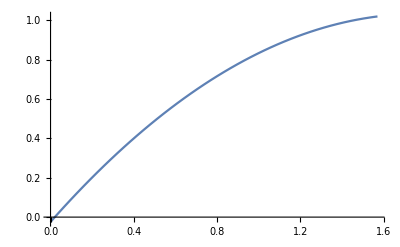

```mathematica
Plot[g, {x, 0, Pi/2}]
```

```mathematica
(* равномерно *)
Maximize[{Abs[res[x] - f[x]], x≥ 0, x ≤ Pi/2}, x]
```

{0.0243249,{x→0.}}

```mathematica
(* средно квадратично *)
```

```mathematica
Sqrt[Integrate[(res[x] - f[x])^2, {x, 0, Pi/2}]]
```

0.0105051